# dipole traps

## two level AC stark

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Haf = ({{0, -Ω/2}, {-Ω/2, Δ}});
```

```mathematica
Eigensystem[Haf]
```

{{1/2 (Δ-√(Δ^2+Ω^2)),1/2 (Δ+√(Δ^2+Ω^2))},{{-(-Δ-√(Δ^2+Ω^2))/Ω,1},{-(-Δ+√(Δ^2+Ω^2))/Ω,1}}}

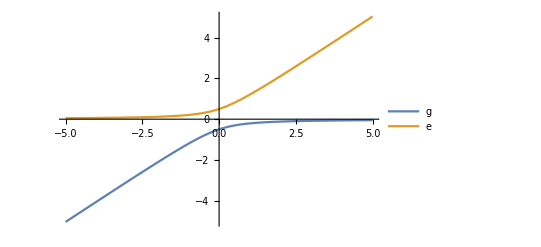

```mathematica
(*Δ=-1;*)
Ω=1;
Plot[{1/2 (Δ-√(Δ^2+Ω^2)),1/2 (Δ+√(Δ^2+Ω^2))},{Δ,-5,5},PlotRange->All,Axes->True,PlotLegends->{"g","e"}]
```

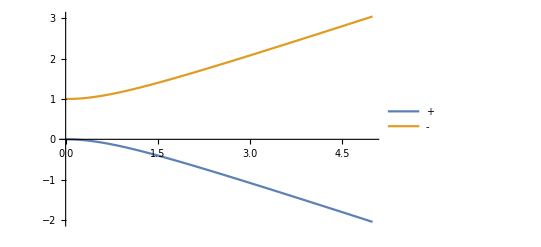

```mathematica
Δ=1;
Plot[{1/2 (Δ-√(Δ^2+Ω^2)),1/2 (Δ+√(Δ^2+Ω^2))},{Ω,0,5},PlotRange->All,Axes->True,PlotLegends->{"+","-"}]
```

```mathematica
Plot[{1/2 (Δ-√(Δ^2+Ω^2)),1/2 (Δ+√(Δ^2+Ω^2))},{Ω,0,5},PlotRange->All,Axes->True,PlotLegends->{"g","e"}]
```

```mathematica
√(Δ^2+Ω^2)
```

```mathematica
Δ √(1+Ω^2/Δ^2)-> Δ + Ω^2/(2Δ)
```

Psuedo potential from AC Stark shift in two-level atom. These are plots of the ground state AC stark shift, with a red detuning

```mathematica
Clear[Δ]
```

```mathematica
(1-Exp[-x^2])^2
```

(1-ⅇ^(-x^2))^2

6

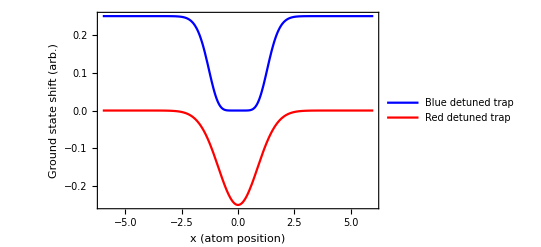

```mathematica
wb=1;wr=6
plt=Show[Plot[ {(((1-Exp[-x^2/wb])^2)^2)/(4 Δ)/.Δ-> 1,((Exp[-2 x^2/wr])^2)/(4 Δ)/.Δ-> -1},{x,-6,6},PlotRange->All,Axes->True,PlotLegends->{"Blue detuned trap","Red detuned trap"},PlotStyle->{Blue,Red},Frame->{True,True,False,False},FrameLabel-> {"x (atom position)","Ground state shift (arb.)"},LabelStyle->Directive[Black,FontSize-> 14]],Axes-> False]
```

```mathematica
Export["1trap_2trap_redtrap_bluetrap.png",plt]
```

1trap_2trap_redtrap_bluetrap.png

## gaussian beam profile

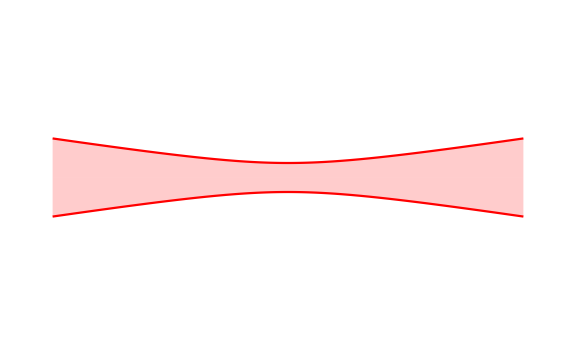

```mathematica
α=5;
plt=Plot[{α √(1+z^2),-α √(1+z^2)},{z,-2.5,2.5},PlotStyle->Hue[1],Filling-> Axis,Axes->False,PlotRange->{-50,50},ImageSize->Large]
```

```mathematica
Export["FORT_site_big.png",plt,ImageResolution-> 600]
```

FORT_site_big.png

```mathematica
reds = Table[Hue[1,1.0/(1+(0.5i)^2)],{i,{-2,-1,0,1,2}}]
```

{Hue[1, 0.5],Hue[1, 0.8],Hue[1, 1.],Hue[1, 0.8],Hue[1, 0.5]}

```mathematica
plts=Table[Plot[{2 √(1+z^2)-10i,-2 √(1+z^2)-10i},{z,-5,5},PlotStyle->Hue[1,1./(1+(0.5i)^2)],Filling->{1-> {2}},Axes->False,PlotRange->{-50,50},ImageSize->Large],{i,{-2,-1,0,1,2}}];
AppendTo[plts,Plot[Evaluate[{If[z>0,0.8*2 √(1+z^2)-10i],If[z>0,-0.8*2 √(1+z^2)-10i]}/.i-> 1],{z,-5,5},PlotStyle->Hue[0.54,1],Filling->{1-> {2}},FillingStyle-> Opacity[0.9],Axes->False,ImageSize->Large]];
AppendTo[plts,Plot[Evaluate[{If[z<=0,0.8*2 √(1+z^2)-10i],If[z<=0,-0.8*2 √(1+z^2)-10i]}/.i-> 1],{z,-5,5},PlotStyle->Hue[1,0.8],Filling->{1-> {2}},FillingStyle-> Opacity[0.9],Axes->False,ImageSize->Large]];
```

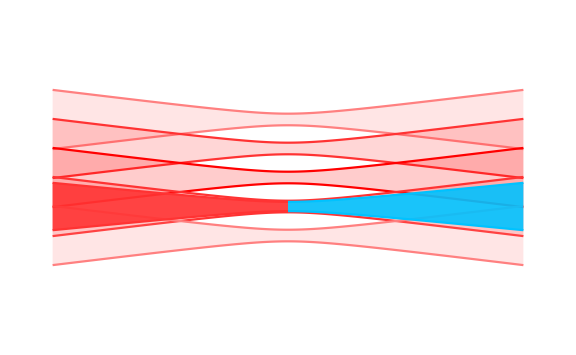

```mathematica
plt =Show[plts,ImageSize-> Large]
```

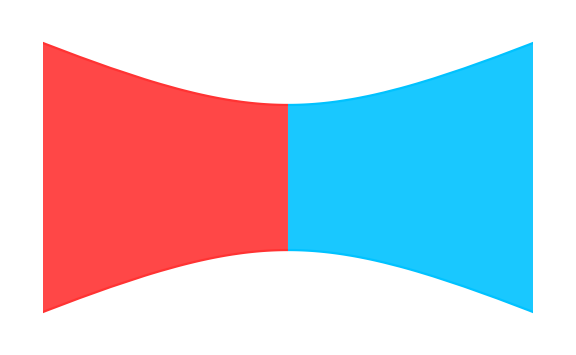

```mathematica
plts={};
AppendTo[plts,Plot[Evaluate[{If[z>0,2 √(1+z^2)],If[z>0,-2 √(1+z^2)]}/.i-> 1],{z,-5,5},PlotStyle->Hue[0.54,1],Filling->{1-> {2}},FillingStyle-> Opacity[0.9],Axes->False,ImageSize->Large]];
AppendTo[plts,Plot[Evaluate[{If[z<=0,2 √(1+z^2)],If[z<=0,-2 √(1+z^2)]}/.i-> 1],{z,-5,5},PlotStyle->Hue[1,0.8],Filling->{1-> {2}},FillingStyle-> Opacity[0.9],Axes->False,ImageSize->Large]];
plt =Show[plts,ImageSize-> Large,PlotRange-> {{-1.5,1.5},{-4,4}}]
```

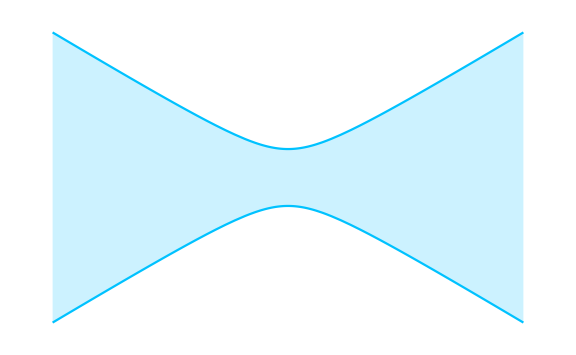

```mathematica
Plot[{2 √(1+z^2)-10,-2 √(1+z^2)-10},{z,-5,5},PlotStyle->Hue[0.54,1],Filling->{1-> {2}},Axes->False,ImageSize->Large]
```

```mathematica
Export["rydberg_beams_huge.png",plt,ImageResolution-> 200]
```

rydberg_beams_huge.png

```mathematica
ColorData["DarkRainbow"][[-1]][0.9]
```

RGBColor[0.72987, 0.239399, 0.230961]

```mathematica
Hue[0.54,0.8]
```

Hue[0.54, 0.8]

```mathematica
Hue[1,0.8]
```

Hue[1, 0.8]

```mathematica
1.7*^9/10
```

1.7×10^8

```mathematica
1.
```